```mathematica
(*изотропный материал с эллиптическими включениями*)

Fun2[x_]:=Module[{y={{C11,C12,C12,0,0,0},{C12,C11,C12,0,0,0},{C12,C12,C11,0,0,0},{0,0,0,(C11-C12)/2,0,0},{0,0,0,0,(C11-C12)/2,0},{0,0,0,0,0,(C11-C12)/2}}},
y=x;
y[[4]]=2*y[[4]];
y[[5]]=2*y[[5]];
y[[6]]=2*y[[6]];
Return[y];
];
Fun4[x_]:=Module[{y={{C11,C12,C12,0,0,0},{C12,C11,C12,0,0,0},{C12,C12,C11,0,0,0},{0,0,0,(C11-C12)/2,0,0},{0,0,0,0,(C11-C12)/2,0},{0,0,0,0,0,(C11-C12)/2}}},
y=x;
y[[4]]=4*y[[4]];
y[[5]]=4*y[[5]];
y[[6]]=4*y[[6]];
Return[y];
];
Fun05[x_]:=Module[{y={{C11,C12,C12,0,0,0},{C12,C11,C12,0,0,0},{C12,C12,C11,0,0,0},{0,0,0,(C11-C12)/2,0,0},{0,0,1,0,(C11-C12)/2,0},{0,0,0,0,0,(C11-C12)/2}}},
y=x;
y[[4]]=0.5*y[[4]];
y[[5]]=0.5*y[[5]];
y[[6]]=0.5*y[[6]];
Return[y];
];
Ee=3*10^9;
v=0.3;
C11=(Ee(1-v))/((1+v)(1-2v));
C12=(Ee*v)/((1+v)(1-2v));
Cmatr={{C11,C12,C12,0,0,0},{C12,C11,C12,0,0,0},{C12,C12,C11,0,0,0},{0,0,0,(C11-C12)/2,0,0},{0,0,0,0,(C11-C12)/2,0},{0,0,0,0,0,(C11-C12)/2}};
K1=Ee/(3*(1-2*v));
mu1=Ee/(2*(1+v));
MatrixForm[Cmatr]
```

(4.03846×10^9 | 1.73077×10^9 | 1.73077×10^9 | 0 | 0 | 0
1.73077×10^9 | 4.03846×10^9 | 1.73077×10^9 | 0 | 0 | 0
1.73077×10^9 | 1.73077×10^9 | 4.03846×10^9 | 0 | 0 | 0
0 | 0 | 0 | 1.15385×10^9 | 0 | 0
0 | 0 | 0 | 0 | 1.15385×10^9 | 0
0 | 0 | 0 | 0 | 0 | 1.15385×10^9)

```mathematica
Ee1=55*10^9;
v1=0.2;
C11=(Ee1(1-v1))/((1+v1)(1-2v1));
C12=(Ee1*v1)/((1+v1)(1-2v1));
Cmatr2={{C11,C12,C12,0,0,0},{C12,C11,C12,0,0,0},{C12,C12,C11,0,0,0},{0,0,0,(C11-C12)/2,0,0},{0,0,0,0,(C11-C12)/2,0},{0,0,0,0,0,(C11-C12)/2}};
K2=Ee1/(3*(1-2*v1));
mu2=Ee1/(2*(1+v1));
MatrixForm[Cmatr2]
```

(6.11111×10^10 | 1.52778×10^10 | 1.52778×10^10 | 0 | 0 | 0
1.52778×10^10 | 6.11111×10^10 | 1.52778×10^10 | 0 | 0 | 0
1.52778×10^10 | 1.52778×10^10 | 6.11111×10^10 | 0 | 0 | 0
0 | 0 | 0 | 2.29167×10^10 | 0 | 0
0 | 0 | 0 | 0 | 2.29167×10^10 | 0
0 | 0 | 0 | 0 | 0 | 2.29167×10^10)

```mathematica
a1=3;
a2=1;
a3=1;
I2=(2π*a1*a2^2)/((a1^2-a2^2)^(3/2))*(a1/a2(a1^2/a2^2-1)^(1/2)-N@ArcCosh[a1/a2]);
I1=4π-2I2;
I12=(I2-I1)/(a1^2-a2^2);
I11=(4π)/(3 a1^2)-(2I12)/3;
I22=π/a2^2-(I2-I1)/(4(a1^2-a2^2));
s11=(3 a1^2)/(8π(1-v))*I11+(1-2v)/(8π(1-v))I1;
s22=s33=(3 a1^2)/(8π(1-v))*I22+(1-2v)/(8π(1-v))I2;
s55=s66=(a1^2+a2^2)/(16π(1-v))I12+(1-2v)/(16π(1-v))(I1+I2);
s44=a2^2/(8π(1-v))I22+(1-2v)/(8π(1-v))(I2);
s12=s13=a2^2/(8π(1-v))I12-(1-2v)/(8π(1-v))I1;
s21=s31=(5*v-1)/(15*(1-v));
s32=(5*v-1)/(15*(1-v));
s23=a2^2/(8π(1-v))I22-(1-2v)/(8π(1-v))(I2);

S={{s11,s12,s13,0,0,0},{s21,s22,s23,0,0,0},{s31,s32,s33,0,0,0},{0,0,0,s44,0,0},{0,0,0,0,s55,0},{0,0,0,0,0,s66}};
MatrixForm[S]
```

(0.203842 | -0.000976293 | -0.000976293 | 0 | 0 | 0
0.047619 | 4.74569 | 0.0437233 | 0 | 0 | 0
0.047619 | 0.047619 | 4.74569 | 0 | 0 | 0
0 | 0 | 0 | 0.298378 | 0 | 0
0 | 0 | 0 | 0 | 0.229611 | 0
0 | 0 | 0 | 0 | 0 | 0.229611)

```mathematica
T1=Inverse[Fun4[(Fun05[IdentityMatrix[6]]+(S.(Fun2[Inverse[Fun4[Cmatr]]]).(Fun2[Cmatr2-Cmatr])))]];

MatrixForm[T1]
```

(0.241063 | 0.00192289 | 0.00192446 | 0. | 0. | 0.
0.0412675 | 0.0133989 | 0.00225053 | 0. | 0. | 0.
0.0412695 | 0.00223965 | 0.0134009 | 0. | 0. | 0.
0. | 0. | 0. | 0.0407981 | 0. | 0.
0. | 0. | 0. | 0. | 0.0517521 | 0.
0. | 0. | 0. | 0. | 0. | 0.0517521)

```mathematica
c1=0.3;
c0=0.7;
eps=Inverse[Fun4[(c0*Fun05[IdentityMatrix[6]]+c1*T1)]];

A1=T1.Fun2[eps];
MatrixForm[A1]
```

(0.312049 | 0.00247324 | 0.00247526 | 0. | 0. | 0.
0.0530787 | 0.0189855 | 0.00313495 | 0. | 0. | 0.
0.0530814 | 0.00311962 | 0.0189882 | 0. | 0. | 0.
0. | 0. | 0. | 0.0563137 | 0. | 0.
0. | 0. | 0. | 0. | 0.0707913 | 0.
0. | 0. | 0. | 0. | 0. | 0.0707913)

```mathematica
A0=Inverse[Fun4[c0*Fun05[IdentityMatrix[6]]-c1*T1]];
MatrixForm[A0]
```

(1.59322 | 0.00132182 | 0.00132291 | 0. | 0. | 0.
0.028368 | 1.43685 | 0.0014174 | 0. | 0. | 0.
0.0283693 | 0.00141064 | 1.43685 | 0. | 0. | 0.
0. | 0. | 0. | 0.740169 | 0. | 0.
0. | 0. | 0. | 0. | 0.747441 | 0.
0. | 0. | 0. | 0. | 0. | 0.747441)

```mathematica
Ccomp=Cmatr+(c1*(Cmatr2-Cmatr)).Fun2[A1];
MatrixForm[Ccomp]
```

(9.81275×10^9 | 1.86295×10^9 | 1.86306×10^9 | 0. | 0. | 0.
4.1235×10^9 | 4.38626×10^9 | 1.87168×10^9 | 0. | 0. | 0.
4.12354×10^9 | 1.87139×10^9 | 4.38637×10^9 | 0. | 0. | 0.
0. | 0. | 0. | 1.88917×10^9 | 0. | 0.
0. | 0. | 0. | 0. | 2.07822×10^9 | 0.
0. | 0. | 0. | 0. | 0. | 2.07822×10^9)

```mathematica
lst={};
lstl={100};
lstj={100};
lstk={100};
V=a1*a2*a3*π*4/3;
Vgen=5^3*5*3*3;
n=IntegerPart[N@((0.3*Vgen)/V)]+1;
u=0;
For[i=0,i<n,i++,
l=RandomReal[{0,25}];

j=RandomReal[{0,15}];

k=RandomReal[{0,15}];
Flag=True;
For[e=1,e<=Length[lstl],e++,
If[(Abs[lstl[[e]]-l]>1.9*a1)||(Abs[lstj[[e]]-j]>1.9*a2)||(Abs[lstk[[e]]-k]>1.9*a3),o=0,Flag=False];];
If[Flag,
AppendTo[lstl,l];
AppendTo[lstj,j];
AppendTo[lstk,k];
AppendTo[lst,Ellipsoid[{l,j,k},{a1,a2,a3}]],
i--];
];
u
Length[lstl];
lstl;
lst;
Graphics3D[lst]
```

0

-Graphics3D-

```mathematica
Enew=((Ccomp[[1]][[1]])^2+Ccomp[[1]][[1]]-2*(Ccomp[[1]][[2]])^2)/(Ccomp[[1]][[1]]+Ccomp[[1]][[2]])
vnew=(Ccomp[[1]][[2]])/(Ccomp[[1]][[1]]+Ccomp[[1]][[2]])
K_Teor=K1+(c1*K1*(K2-K1)*(3*K1+4*mu1))/(3*(1-c1)*(K2-K1)*K1+K2*(3*K1+4*mu1))
mu_Teor=mu1+(5*c1*mu1*(mu2-mu1)*(3K1+4*mu1))/(6*(1-c1)(mu2-mu1)(K1+2mu1)+5*mu2*(3K1+4mu1))
Knew=Enew/(3*(1-2vnew))
munew=Enew/(2*(1+vnew))
```

7.65255×10^9

0.159558

2.99263×10^9

1.40353×10^9

3.74638×10^9

3.29977×10^9

```mathematica
3.2997706789700294*^9
```

3.29977×10^9

```mathematica
Find_composit[c_]:=Module[{Ee=3*10^9,v=0.3,Ee1=55*10^9,v1=0.2,a1=3,a2=1,a3=1,c1=c,c0=1-c,Enew,vnew,Knew,munew},


C11=(Ee(1-v))/((1+v)(1-2v));
C12=(Ee*v)/((1+v)(1-2v));
Cmatr={{C11,C12,C12,0,0,0},{C12,C11,C12,0,0,0},{C12,C12,C11,0,0,0},{0,0,0,(C11-C12)/2,0,0},{0,0,0,0,(C11-C12)/2,0},{0,0,0,0,0,(C11-C12)/2}};
K1=Ee/(3*(1-2*v));
mu1=Ee/(2*(1+v));
MatrixForm[Cmatr];

C11=(Ee1(1-v1))/((1+v1)(1-2v1));
C12=(Ee1*v1)/((1+v1)(1-2v1));
Cmatr2={{C11,C12,C12,0,0,0},{C12,C11,C12,0,0,0},{C12,C12,C11,0,0,0},{0,0,0,(C11-C12)/2,0,0},{0,0,0,0,(C11-C12)/2,0},{0,0,0,0,0,(C11-C12)/2}};
K2=Ee1/(3*(1-2*v1));
mu2=Ee1/(2*(1+v1));
MatrixForm[Cmatr2];
a1=3;
a2=1;
a3=1;
I2=(2π*a1*a2^2)/((a1^2-a2^2)^(3/2))*(a1/a2(a1^2/a2^2-1)^(1/2)-N@ArcCosh[a1/a2]);
I1=4π-2I2;
I12=(I2-I1)/(a1^2-a2^2);
I11=(4π)/(3 a1^2)-(2I12)/3;
I22=π/a2^2-(I2-I1)/(4(a1^2-a2^2));
s11=(3 a1^2)/(8π(1-v))*I11+(1-2v)/(8π(1-v))I1;
s22=s33=(3 a1^2)/(8π(1-v))*I22+(1-2v)/(8π(1-v))I2;
s55=s66=(a1^2+a2^2)/(16π(1-v))I12+(1-2v)/(16π(1-v))(I1+I2);
s44=a2^2/(8π(1-v))I22+(1-2v)/(8π(1-v))(I2);
s12=s13=a2^2/(8π(1-v))I12-(1-2v)/(8π(1-v))I1;
s21=s31=(5*v-1)/(15*(1-v));
s32=(5*v-1)/(15*(1-v));
s23=a2^2/(8π(1-v))I22-(1-2v)/(8π(1-v))(I2);

S={{s11,s12,s13,0,0,0},{s21,s22,s23,0,0,0},{s31,s32,s33,0,0,0},{0,0,0,s44,0,0},{0,0,0,0,s55,0},{0,0,0,0,0,s66}};
MatrixForm[S];
T1=Inverse[Fun4[(Fun05[IdentityMatrix[6]]+(S.(Fun2[Inverse[Fun4[Cmatr]]]).(Fun2[Cmatr2-Cmatr])))]];

MatrixForm[T1];

eps=Inverse[Fun4[(c0*Fun05[IdentityMatrix[6]]+c1*T1)]];

A1=T1.Fun2[eps];
MatrixForm[A1];
A0=Inverse[Fun4[c0*Fun05[IdentityMatrix[6]]-c1*T1]];
MatrixForm[A0];
Ccomp=Cmatr+(c1*(Cmatr2-Cmatr)).Fun2[A1];
MatrixForm[Ccomp];
Enew=((Ccomp[[1]][[1]])^2+Ccomp[[1]][[1]]-2*(Ccomp[[1]][[2]])^2)/(Ccomp[[1]][[1]]+Ccomp[[1]][[2]]);
vnew=(Ccomp[[1]][[2]])/(Ccomp[[1]][[1]]+Ccomp[[1]][[2]]);
K_Teor=K1+(c1*K1*(K2-K1)*(3*K1+4*mu1))/(3*(1-c1)*(K2-K1)*K1+K2*(3*K1+4*mu1));
mu_Teor=mu1+(5*c1*mu1*(mu2-mu1)*(3K1+4*mu1))/(6*(1-c1)(mu2-mu1)(K1+2mu1)+5*mu2*(3K1+4mu1));
Knew=Enew/(3*(1-2vnew));
munew=Enew/(2*(1+vnew));

Return[{Enew,vnew,Knew,munew}];
];
m={};
m=Find_composit[0.3];
m[[1]]
```

0.3

```mathematica
(*ДЛЯ ЭЛЛИПСОИДА*)
vecE=vecv=vecK=vecmu={};
For[i=0,i<=100,i++,
Ee=3*10^9;
v=0.3;
Ee1=55*10^9;
v1=0.2;
a1=3;
a2=1;
a3=1;
c1=i/100;
c0=1-c1;
C11=(Ee(1-v))/((1+v)(1-2v));
C12=(Ee*v)/((1+v)(1-2v));
Cmatr={{C11,C12,C12,0,0,0},{C12,C11,C12,0,0,0},{C12,C12,C11,0,0,0},{0,0,0,(C11-C12)/2,0,0},{0,0,0,0,(C11-C12)/2,0},{0,0,0,0,0,(C11-C12)/2}};
K1=Ee/(3*(1-2*v));
mu1=Ee/(2*(1+v));
MatrixForm[Cmatr];

C11=(Ee1(1-v1))/((1+v1)(1-2v1));
C12=(Ee1*v1)/((1+v1)(1-2v1));
Cmatr2={{C11,C12,C12,0,0,0},{C12,C11,C12,0,0,0},{C12,C12,C11,0,0,0},{0,0,0,(C11-C12)/2,0,0},{0,0,0,0,(C11-C12)/2,0},{0,0,0,0,0,(C11-C12)/2}};
K2=Ee1/(3*(1-2*v1));
mu2=Ee1/(2*(1+v1));
MatrixForm[Cmatr2];
a1=3;
a2=1;
a3=1;
I2=(2π*a1*a2^2)/((a1^2-a2^2)^(3/2))*(a1/a2(a1^2/a2^2-1)^(1/2)-N@ArcCosh[a1/a2]);
I1=4π-2I2;
I12=(I2-I1)/(a1^2-a2^2);
I11=(4π)/(3 a1^2)-(2I12)/3;
I22=π/a2^2-(I2-I1)/(4(a1^2-a2^2));
s11=(3 a1^2)/(8π(1-v))*I11+(1-2v)/(8π(1-v))I1;
s22=s33=(3 a1^2)/(8π(1-v))*I22+(1-2v)/(8π(1-v))I2;
s55=s66=(a1^2+a2^2)/(16π(1-v))I12+(1-2v)/(16π(1-v))(I1+I2);
s44=a2^2/(8π(1-v))I22+(1-2v)/(8π(1-v))(I2);
s12=s13=a2^2/(8π(1-v))I12-(1-2v)/(8π(1-v))I1;
s21=s31=(5*v-1)/(15*(1-v));
s32=(5*v-1)/(15*(1-v));
s23=a2^2/(8π(1-v))I22-(1-2v)/(8π(1-v))(I2);

S={{s11,s12,s13,0,0,0},{s21,s22,s23,0,0,0},{s31,s32,s33,0,0,0},{0,0,0,s44,0,0},{0,0,0,0,s55,0},{0,0,0,0,0,s66}};
MatrixForm[S];
T1=Inverse[Fun4[(Fun05[IdentityMatrix[6]]+(S.(Fun2[Inverse[Fun4[Cmatr]]]).(Fun2[Cmatr2-Cmatr])))]];

MatrixForm[T1];

eps=Inverse[Fun4[(c0*Fun05[IdentityMatrix[6]]+c1*T1)]];

A1=T1.Fun2[eps];
MatrixForm[A1];
A0=Inverse[Fun4[c0*Fun05[IdentityMatrix[6]]-c1*T1]];
MatrixForm[A0];
Ccomp=Cmatr+(c1*(Cmatr2-Cmatr)).Fun2[A1];
MatrixForm[Ccomp];
Enew=((Ccomp[[1]][[1]])^2+Ccomp[[1]][[1]]-2*(Ccomp[[1]][[2]])^2)/(Ccomp[[1]][[1]]+Ccomp[[1]][[2]]);
vnew=(Ccomp[[1]][[2]])/(Ccomp[[1]][[1]]+Ccomp[[1]][[2]]);
K_Teor=K1+(c1*K1*(K2-K1)*(3*K1+4*mu1))/(3*(1-c1)*(K2-K1)*K1+K2*(3*K1+4*mu1));
mu_Teor=mu1+(5*c1*mu1*(mu2-mu1)*(3K1+4*mu1))/(6*(1-c1)(mu2-mu1)(K1+2mu1)+5*mu2*(3K1+4mu1));
Knew=Enew/(3*(1-2vnew));
munew=Enew/(2*(1+vnew));
AppendTo[vecE,Enew];
AppendTo[vecv,vnew];
AppendTo[vecK,Knew];
AppendTo[vecmu,munew];

];
```

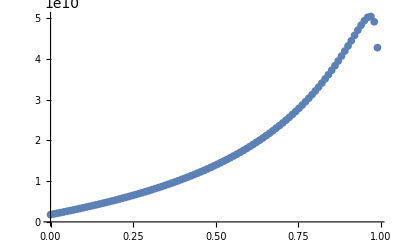

```mathematica
x={};
For[i=0,i<Length[vecE],i++,
AppendTo[x,i/Length[vecE]];
]
ListPlot[Table[{x[[i]],vecE[[i]]},{i,Length[x]}]]
```

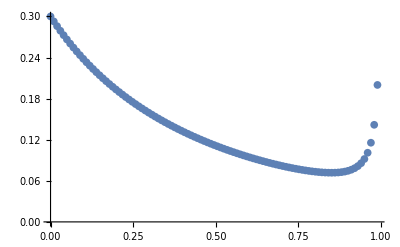

```mathematica
ListPlot[Table[{x[[i]],vecv[[i]]},{i,Length[x]}]]
```

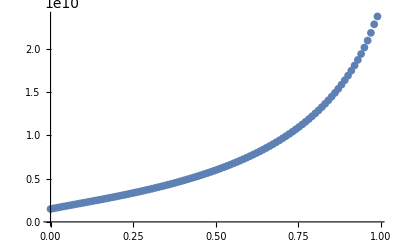

```mathematica
ListPlot[Table[{x[[i]],vecK[[i]]},{i,Length[x]}]]
```

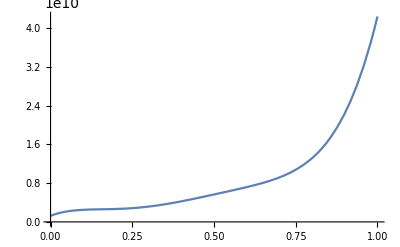

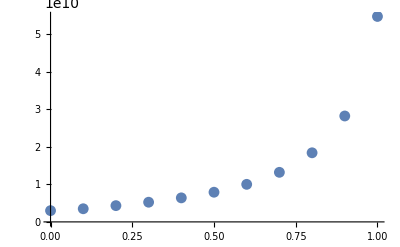

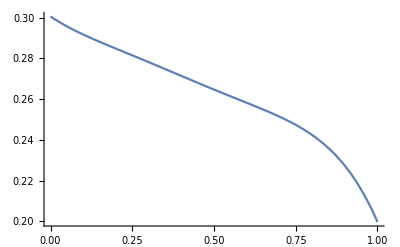

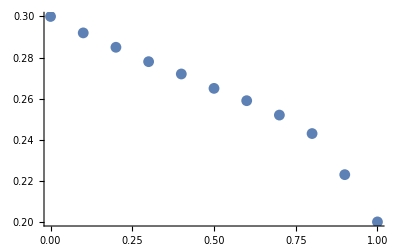

```mathematica
(*ДЛЯ СФЕРЫ*)
vecE=vecv=vecK=vecmu={};
For[i=0,i<=100,i++,
Ee=3*10^9;
v=0.3;
Ee1=55*10^9;
v1=0.2;
a1=1;
a2=1;
a3=1;
c1=i/100;
c0=1-c1;
C11=(Ee(1-v))/((1+v)(1-2v));
C12=(Ee*v)/((1+v)(1-2v));
Cmatr={{C11,C12,C12,0,0,0},{C12,C11,C12,0,0,0},{C12,C12,C11,0,0,0},{0,0,0,(C11-C12)/2,0,0},{0,0,0,0,(C11-C12)/2,0},{0,0,0,0,0,(C11-C12)/2}};
K1=Ee/(3*(1-2*v));
mu1=Ee/(2*(1+v));
MatrixForm[Cmatr];

C11=(Ee1(1-v1))/((1+v1)(1-2v1));
C12=(Ee1*v1)/((1+v1)(1-2v1));
Cmatr2={{C11,C12,C12,0,0,0},{C12,C11,C12,0,0,0},{C12,C12,C11,0,0,0},{0,0,0,(C11-C12)/2,0,0},{0,0,0,0,(C11-C12)/2,0},{0,0,0,0,0,(C11-C12)/2}};
K2=Ee1/(3*(1-2*v1));
mu2=Ee1/(2*(1+v1));
MatrixForm[Cmatr2];
a1=1;
a2=1;
a3=1;
s11=s22=s33=(7-5v)/(15(1-v));
s12=s23=s31=s13=s21=s32=(5v-1)/(15(1-v));
s44=s55=s66=(4-5v)/(15(1-v));

S={{s11,s12,s13,0,0,0},{s21,s22,s23,0,0,0},{s31,s32,s33,0,0,0},{0,0,0,s44,0,0},{0,0,0,0,s55,0},{0,0,0,0,0,s66}};
MatrixForm[S];
T1=Inverse[Fun4[(Fun05[IdentityMatrix[6]]+(S.(Fun2[Inverse[Fun4[Cmatr]]]).(Fun2[Cmatr2-Cmatr])))]];

MatrixForm[T1];

eps=Inverse[Fun4[(c0*Fun05[IdentityMatrix[6]]+c1*T1)]];

A1=T1.Fun2[eps];
MatrixForm[A1];
A0=Inverse[Fun4[c0*Fun05[IdentityMatrix[6]]-c1*T1]];
MatrixForm[A0];
Ccomp=Cmatr+(c1*(Cmatr2-Cmatr)).Fun2[A1];
MatrixForm[Ccomp];
Enew=((Ccomp[[1]][[1]])^2+Ccomp[[1]][[1]]-2*(Ccomp[[1]][[2]])^2)/(Ccomp[[1]][[1]]+Ccomp[[1]][[2]]);
vnew=(Ccomp[[1]][[2]])/(Ccomp[[1]][[1]]+Ccomp[[1]][[2]]);
KTeor=K1+(c1*K1*(K2-K1)*(3*K1+4*mu1))/(3*(1-c1)*(K2-K1)*K1+K2*(3*K1+4*mu1));
muTeor=mu1+(5*c1*mu1*(mu2-mu1)*(3K1+4*mu1))/(6*(1-c1)(mu2-mu1)(K1+2mu1)+5*mu2*(3K1+4mu1));
Knew=Enew/(3*(1-2vnew));
munew=Enew/(2*(1+vnew));
AppendTo[vecE,Enew];
AppendTo[vecv,vnew];
AppendTo[vecK,Knew];
AppendTo[vecmu,munew];

];

x={};
dataE={};
datav={};
For[i=0,i<Length[vecE],i++,
AppendTo[x,i/Length[vecE]];
];
For[i=1,i<Length[vecE],i++,
AppendTo[dataE,{x[[i]],vecE[[i]]}];
AppendTo[datav,{x[[i]],vecv[[i]]}];
];
(*Апроксимируем графики изходя из полученных точек многочленом 5 степени*)
fitE=LinearModelFit[dataE,{y,y^2,y^3,y^4,y^5},y];
fitv=LinearModelFit[datav,{y,y^2,y^3,y^4,y^5},y];
DigimatDataE={{0,3*10^9},{0.1,3.5*10^9},{0.2,4.33*10^9},{0.3,5.24*10^9},{0.4,6.4*10^9},{0.5,7.9*10^9},{0.6,10*10^9},{0.7,13.2*10^9},{0.8,18.4*10^9},{0.9,28.2*10^9},{1,5.47*10^10}};
DigimatDatav={{0,0.3},{0.1,0.292},{0.2,0.285},{0.3,0.278},{0.4,0.272},{0.5,0.265},{0.6,0.259},{0.7,0.252},{0.8,0.243},{0.9,0.223},{1,0.2}};
(**)
Plot[fitE[y],{y,0,1}]
ListPlot[Table[{DigimatDataE[[i]][[1]],DigimatDataE[[i]][[2]]},{i,Length[DigimatDataE]}]]
Plot[fitv[y],{y,0,1}]
ListPlot[Table[{DigimatDatav[[i]][[1]],DigimatDatav[[i]][[2]]},{i,Length[DigimatDatav]}]]
(*ListPlot[Table[{x[[i]],vecE[[i]]},{i,Length[x]}]]*)
(*ListPlot[Table[{x[[i]],vecv[[i]]},{i,Length[x]}]]*)

(*ListPlot[Table[{x[[i]],vecK[[i]]},{i,Length[x]}]]*)
(*ListPlot[Table[{x[[i]],vecmu[[i]]},{i,Length[x]}]]*)
```